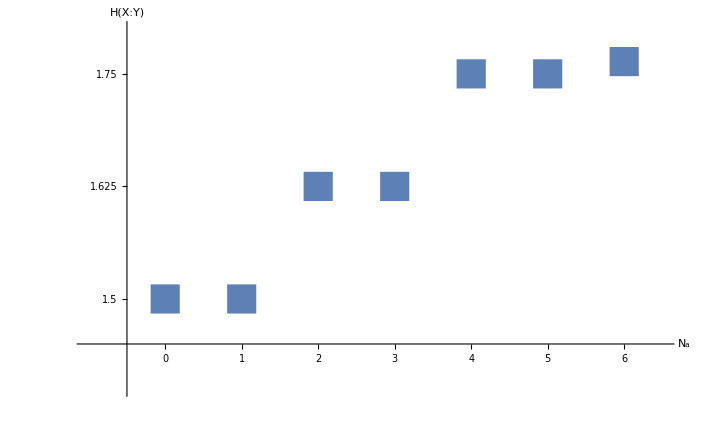

```mathematica
data = {{0,1.5},{1,1.5},{2,1.625},{3,1.625},{4,1.75},{5,1.75},{6,1.76364623755789}};
ListPlot[data,LabelStyle->{FontSize-> 30},AxesLabel->{Subscript["N","a"],"H(X:Y)"},PlotMarkers->{{■,30}},Ticks->{{0,1,2,3,4,5,6},{1.50,1.625,1.75,1.875,2.0}},PlotRange->{{-1,6.5},{1.4,1.8}},AxesOrigin->{-.5,1.45}]
```

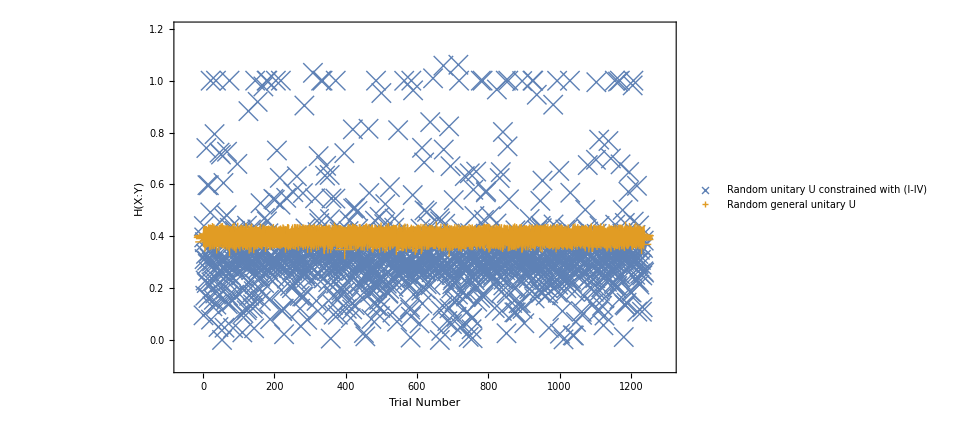

```mathematica
data = Import["/home/jake/Desktop/global-channel-optimization/conditionedU.dat","Table"];
data1= Import["/home/jake/Desktop/global-channel-optimization/UnconditionedU.dat","Table"];
ListPlot[{data,data1},LabelStyle->{FontSize-> 30},AxesLabel->{"Trial Number","H(X:Y)"},PlotMarkers->{{"×",20},{"+",20}},Ticks->{{0,200,400,600,800,1000,1200},{0,0.2,0.4,0.6,0.8,1.0}},PlotRange->{{-55,1300},{-.1,1.2}},AxesOrigin->{-50,-.1},Frame->True,FrameLabel->{"Trial Number","H(X:Y)"},RotateLabel->True,PlotLegends->Placed[PointLegend[Automatic,{Style["Random unitary U constrained with (I-IV)",RGBColor[0,0,0,.7],15],Style["Random general unitary U",RGBColor[0,0,0,.7],15]},LegendFunction->"Frame",Background->White],{0.72,0.155}]]
```

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2 Pi},PlotLegend->{"sine","cosine"},LegendPosition->{0.8,-0.8}]
```

```mathematica
ListLinePlot[Table[f,{f,{Log[x],x^(1/2)}},{x,0,10,0.1}],DataRange->{0,10},PlotLegends->Placed[{"log(x)","\!\(\*SuperscriptBox[\(x\), \(1/2\)]\)"},Above]]
```

```mathematica
PlotLegends-> {Placed[{Style["Random U constrained with (I-IV)",Gray,20],Style["General Random U",Gray,20]},{0.85,0.94}]}
```

```mathematica
ListPlot[{Sqrt[Range[50]],Power[Range[50],(3)^-1]},PlotLegends->PointLegend[Automatic,{"one","two"},LegendFunction->"Frame",LegendLabel->"datasets"]]
```

```mathematica
PlotLegends-> {Placed[{Style["Random U constrained with (I-IV)",Gray,20],Style["General Random U",Gray,20]},{0.85,0.94}]}
```